# Text Learning

```mathematica
labels={"AliceInWonderland","BeowulfModern","DonQuixoteIEnglish","Hamlet","OriginOfSpecies"};
```

```mathematica
texts=Map[{"Text",#}&,labels];
```

```mathematica
rawdata=RandomSample[Flatten[Map[Function[{text},Map[#->Last[text]&,TextSentences[ExampleData[text]]]],texts]]];
```

```mathematica
Length[rawdata]
```

12702

```mathematica
dictionary=WordList[];
```

```mathematica
TextEncoder[string_]:=Module[{words,codes,vector},
words=TextWords[string];
codes=Map[Position[dictionary,#]&,words];
If[Flatten[codes]==={},
vector={},
vector=Flatten[ReplaceAll[codes,{}->0]]
];
Take[Join[vector,ConstantArray[0,100]],100]
]
```

```mathematica
TextEncoder["And, sister, as the winds give benefit And convoy is assistant, do not sleep, But let me hear from you."]
```

{0,31928,1921,35343,0,14754,3161,0,7430,0,2040,10344,23388,32124,0,19933,21252,15974,14120,40047,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data=Map[TextEncoder[First[#]]->Last[#]&,rawdata];
```

```mathematica
training=data[[;;10000]];
validation=data[[10001;;]];
```

```mathematica
training[[1]]
```

{0,31928,1921,35343,0,14754,3161,0,7430,0,2040,10344,23388,32124,0,19933,21252,15974,14120,40047,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→Hamlet

```mathematica
net=NetChain[{1000,Ramp,5,Ramp,SoftmaxLayer[]},"Input"->100,"Output"->NetDecoder[{"Class",labels}]]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
net=NetTrain[net,training,ValidationSet->validation,TargetDevice->"CPU",MaxTrainingRounds->1000]
```

NetChain[]

#### Check it

```mathematica
cm=ClassifierMeasurements[net,validation];
```

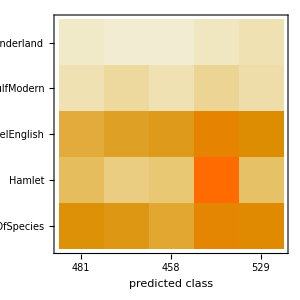

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

0.26943